# Algorimo para la simplificacion del MLC

Creacion del grafo ejemplo

```mathematica
(*SE DEFINEN LAS CONEXIONES*)
nEdges={1<->2,2<->3,2<->5,2<->6,3<->4,3<->7,4<->7,5<->8};
(*SE DEFINEN LOS PESOS*)
eWeigth={16,10,5,2,6,4,4,12};
(*SE DEFINEN LAS COORDENADAS PARA EL POSICIONAMIENTO DE LA GRÁFICA*)
coord={{0,1},{1,2},{1,1},{1,0},{2,2},{2,1},{2,0},{3,1}};
(*SE MAPEAN LAS CONEXINOES CON SUS RESPECTIVOS PESOS*)
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
(*SE GENERA LA GRÁFICA*)
grafo =Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges];
```

Algoritmo para la obtención de la lista de hojas ordenada por peso

```mathematica
(*FUNCION PARA OBTENER LAS HOJAS DEL ARBOL*)
ListOfLefts[S_, V_] := Module[{lefts,g, vertices}, 
g = S;
vertices=V;
lefts= {};
(*SE PROCESA CADA VERTICE*)
For[ x =1, x<=Length[V], x++,
(*SI EL VERTICE CONTIENE SOLO UNA CONEXION, ENTONCES SE TRATA DE UNA HOJA*)
If[VertexDegree[g,V[[x]]] ==1,
(*SE AGREGA A LA LISTA DE VERICES HOJAS*)
AppendTo[lefts, V[[x]] ]
]
];
lefts(*SE RETORNA LA LISTA CON LOS VETICES HOJA*)
]



(*FUNCION PARA OBTENER EL VERTICE CONECTADO AL VERTICE HOJA*)
ListOfConnections[G_,V_]:=Module[{grafo,hojas,connections,auxList}, 
grafo = G;
hojas = V;
connections = {};
auxList={};
(*SE PROCESA CADA VERTICE HOJA*)
For[x=1,x ≤ Length[hojas], x++,
(*VARIABLE AUXILIAR PARA OBTENER LAS CONEXIONES DEL VERTICE HOJA*)
auxList = VertexList[NeighborhoodGraph[grafo, hojas[[x]]]] ;
(*SE AGREGA A LA LISTA DE CONEXIONES, EL SEGUNDO ELEMENTO DE LA LISTA DE CONEXIONES DEL VERTICE HOJA NALIZADO*)
(*EL PRIMER ELEMENTO DE LA VARIABLE DE CONEXIONES DEL VERTICE HOJA, CONTIENE EL VERTCE HOJA*)
AppendTo[connections,auxList[[2]]  ];
];
(*SE RETORNA LA LISTA DE LOS VERTICES CONECTADOS A LOS VERTICES HOJA*)
connections
]

(*FUNCION PARA OBTENER EL PESO DE CADA CONEXION DE LOS VERTICES HOJAS*)
pesos[G_,V_, A_] := Module[{g,origen, destino, pesos},
g = G;
origen = V;
destino = A;
pesos = {};
(*SE PROCESA CADA VERTICE*)
For[x = 1, x≤Length[origen], x++,
(*SE AGREGA A LA LISTA, LA DISTANCIA QUE EXISTE ENTRE EL VERTICE HOJA Y SU VERTICE CONECTADO*)
AppendTo[pesos,IntegerPart[GraphDistance[g,origen[[x]],destino[[x]],Method->"Dijkstra"]]];
];
(*SE RETORNA LA LISTA DE LOS PESOS*)
pesos
]

(*
nEdges={1<->2,2<->3,2<->5,2<->6,3<->4,3<->7,4<->7,5<->8};
eWeigth={16,10,5,2,6,4,4,12};
coord={{0,1},{1,2},{1,1},{1,0},{2,2},{2,1},{2,0},{3,1}};
eEdges=Map[nEdges_⟦#⟧->eWeigth_⟦#⟧&,Range[Length[nEdges]]];
grafo =Graph[nEdges,VertexLabels->"Name",VertexSize->Medium,EdgeWeight->eWeigth,VertexCoordinates->coord,EdgeLabels->eEdges];
*)


getListOfLefts[] :=Module[{hojas,conecciones,newEdges,pesosConexiones, Mapeo},
(*OBTENCION DE LAS HOJAS Y LOS VERTICES CON QUE SE CONECTA CADA UNA*)
hojas = ListOfLefts[grafo, VertexList[grafo]];
conecciones= ListOfConnections[grafo,hojas];
(*SE GENERAN LAS CONEXIONES *)
newEdges= {};
For[x=1, x≤ Length[conecciones], x++,
AppendTo[newEdges, hojas[[x]] <-> conecciones[[x]] ];
];
(*SE OBTIENE LA LISTA DE PESOS ENTRE LAS CONEXIONES*)
pesosConexiones= pesos[grafo, hojas, conecciones];
(*SE GENERA UN MAPEO DE LAS CONECCIONES Y EL PESO ENTRE ELLAS*)
Mapeo= Map[newEdges_⟦#⟧->pesosConexiones_⟦#⟧&, Range[Length[pesosConexiones]]];
Mapeo = SortBy[Mapeo,Last];
(*SE ACOMODAN DE MODO DESCENDENTE*)
Mapeo = Reverse[Mapeo];
Mapeo
]
```

Metodo de reducción

Hojas

{1<->2→16,8<->5→12,6<->2→2}

Grafo original

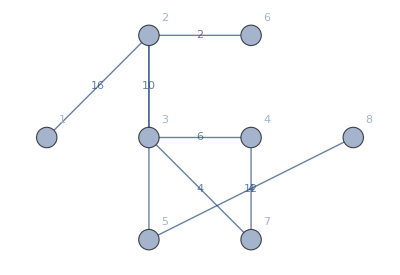

Eliminado de la arista de 1

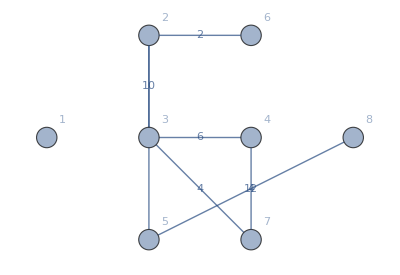

Eliminado del vertice 1

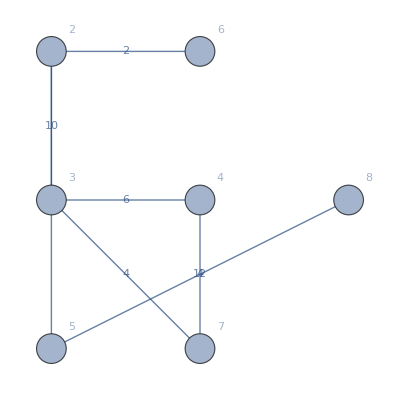

```mathematica
(*
(*OBTENER LA LISTA DE LAS HOJAS DEL ARBOL*)
Print["Hojas"]
hojitas = getListOfLefts[]
Print["Grafo original"]
grafo
(*PRUEBA BORRADO DE ARISTA*)
grafo = EdgeDelete[grafo,hojitas[[1]][[1]]];
Print["Eliminado de la arista de 1"]
grafo
(*PRUEBA BORRADO DE VERTICE*)
grafo = VertexDelete[grafo,hojitas[[1]][[1]][[1]]];
Print["Eliminado del vertice 1"]
grafo

(*FindCycle[grafo]*)
*)






(*METODO DE REDUCCION*)

ReduceMLC[S_, G_] := 
 Module[{aristaEliminada, leaftVertices, R, verticeAux },
  aristaEliminada = false;
  While[aristaEliminada == false,
   leaftVertices = getListOfLefts[];
   For[x = 1, x <= Length[leaftVertices], x++,
    verticeAux = leftVertices[[x]][[1]][[1]];
    R = VertexDelete[S, verticeAux];
    R = EdgeDelete[R, leftVertices[[x]][[1]]];
    If[EsInstanciaMLC[R],
     aristaElminada = true;
     S = R;
     Break[]
     ](*FIN DEL IF*)
    ](*FIN DEL CICLO FOR*)
   ](*FIN DEL CICLO \
WHILE*);
  S
  ](*FIN DE LA FUNCION*)

Nvertices = {1 <-> 2, 1 <-> 11, 2 <-> 12, 2 <-> 3, 3 <-> 4, 4 <-> 5, 
   5 <-> 6, 5 <-> 9, 6 <-> 7, 7 <-> 8, 7 <-> 9, 8 <-> 10, 10 <-> 11, 
   10 <-> 9, 11 <-> 12, 12 <-> 4};
Npesos = {4, 1, 6, 5, 6, 7, 8, 4, 9, 11, 2, 5, 3, 2, 8, 1};
Ncoordenadas = {{0, 3}, {1, 3}, {0, 2}, {1, 2}, {3, 3}, {3, 2}, {3, 
    1}, {3, 0}, {2, 1}, {2, 0}, {0, 0}, {0, 1}};
eVertices = Map[
Nvertices_⟦#⟧ -> 
Npesos_⟦#⟧ &, Range[Length[Nvertices]]];
Poligono = 
  Graph[Nvertices, VertexLabels -> "Name", VertexSize -> Medium, 
   EdgeWeight -> Npesos, VertexCoordinates -> Ncoordenadas, 
   EdgeLabels -> eVertices];
(*
Pick[EdgeList[Poligono],#,1]&/@EdgeCycleMatrix[Poligono];
HighlightGraph[Poligono,#]&/@%*)
(*Ciclos= \
FindFundamentalCycles[Poligono];*)
Ciclos = 
 FindCycle[Poligono, Infinity, All]
(*HighlightGraph[Poligono,%];*)

VertexList[Poligono];
Lista = {};

For[x = 1, x <= Length[VertexList[Poligono]], x++,
 AppendTo[Lista, {VertexList[Poligono][[x]], 0}]
 ]
Lista

Ruta = {};

hermanos = VertexList[NeighborhoodGraph[Poligono, Lista[[1]][[1]]]];
Lista[[1]][[2]] = 1;
hermanos = Delete[hermanos, 1]

Print["If"]
Position[Lista, hermanos[1]]
Lista != {}

If[Position[Lista, hermanos[1]] != {},
 If[MemberQ[Ruta, Lista[[Position[Lista, hermanos[1]]]][[1]]] == 
   True,
  Break[]
  ,
  AppendTo[Ruta, Lista[[Position[Lista, hermanos[1]]]][[1]]];
  ]
 ,
 Print["Lista vacia"]
 ]


Poligono



GetList[L_, h_] := Module[{Lista, hermanos, P},
  Lista = L;
  hermanos = h;
  For[x = 1, x <= Length[hermanos], x++,
   P = Ruta;
   Lista[[Position[Lista, hermanos[x]]]][[2]] = 1;
   If[Position[Lista, hermanos[x]] != {},
    If[MemberQ[Ruta, Lista[[Position[Lista, hermanos[x]]]][[1]]] == 
      True,
     Break[]
     ,
     AppendTo[Ruta, Lista[[Position[Lista, hermanos[1]]]][[1]]];
     ]
    ,
    Print["Lista vacia"]
    ]
   
   ];
  P
  ]

lista = GetList[Lista, hermanos]











(*
HighlightGraph[Poligono,Ciclos[[1]]];
HighlightGraph[Poligono,Ciclos[[2]]];
HighlightGraph[Poligono,Ciclos[[3]]];
HighlightGraph[Poligono,Ciclos[[4]]];
*)
Print["CycleMatix"]
Ciclos
Pick[EdgeList[Poligono], #, 1] & /@ EdgeCycleMatrix[Poligono];
HighlightGraph[Poligono, #] & /@ %
```